NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained -0.000207862-0.00311733 ⅈ and 0.028597 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained -0.000158567-0.00600671 ⅈ and 0.0534642 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained -0.000271598-0.00472392 ⅈ and 0.0418515 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{p[-2]→0.000419692-0.000728202 ⅈ,p[-1]→-0.00209109-0.0003989 ⅈ,p[1]→-0.00195197+0.00136979 ⅈ,p[2]→0.00093154-0.00168465 ⅈ}}

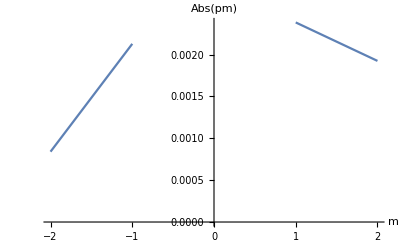

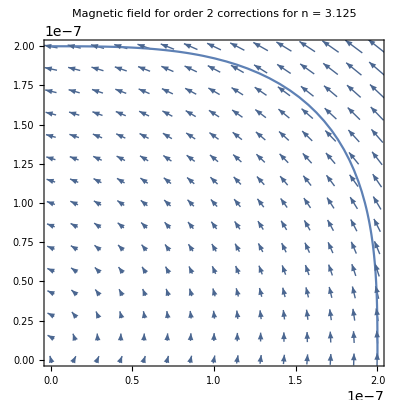

```mathematica
Block[
{M,R,λ,n,Ja,Jb,θ,Br,Bθ,B0,eqn,soln,p,m,k},
M=2;(* Scale of the number of coefficients *)
n=3.125;(* Curvature exponent *)
R=200*10^(-9);(* Size of the conveyor belt cavity *)
λ=110*10^(-9);(* London penetration depth of MgB2 (magnesium diboride) in 4.8 mT and 10.8 K *)
B0=4.8*10^(-3);(* Central magnetic field B0 = 4.8 mT *)
Ja=<||>;Jb=<||>;
For[
k=1,k≤2M,k++,
For[
m=-M,m≤M,m++,Ja=Append[Ja,{m,k}->NIntegrate[BesselI[m,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[I(m-k)θ],{θ,0,2π},Method->"RiemannRule"]];
];
Jb=Append[Jb,k->NIntegrate[BesselI[0,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},Method->"RiemannRule"]];
];
eqn=Table[Jb[k]B0/2+Total[Drop[Table[p[m]Ja[{m,k}],{m,-M,M}],{M+1}]]==0,{k,1,2M}];
soln=NSolve[eqn,Drop[Table[p[m],{m,-M,M}],{M+1}]];
Print[soln];
Print[ListLinePlot[Table[{m,Abs[Part[p[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(pm)"}]];
Br[x_,y_]:=Part[B0/2BesselI[0,Sqrt[x^2+y^2]/λ]+Total[Drop[Table[p[m]BesselI[m,Sqrt[x^2+y^2]/λ]Exp[I m ArcTan[x,y]],{m,-M,M}],{M+1}]]/.soln,1];
Bθ[x_,y_]:=Sqrt[3]B0/2BesselI[0,Sqrt[x^2+y^2]/λ];
Show[VectorPlot[{Re[(Br[x,y] x-Bθ[x,y] y)/Sqrt[x^2+y^2]],Re[(Br[x,y] y+Bθ[x,y] x)/Sqrt[x^2+y^2]]},{x,0.001R,0.999R},{y,0.001R,0.999R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Magnetic field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.50938}. NIntegrate obtained 0.000218098-0.000293022 ⅈ and 0.00680529 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained -0.000207862-0.00311733 ⅈ and 0.028597 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained -0.000158567-0.00600671 ⅈ and 0.0534642 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{p[-3]→-0.000172348+0.00779375 ⅈ,p[-2]→0.00231507-0.00318049 ⅈ,p[-1]→-0.0028129+0.000910924 ⅈ,p[1]→-0.0017451+0.000552681 ⅈ,p[2]→0.00100699+0.00119592 ⅈ,p[3]→-0.00193397-0.00283612 ⅈ}}

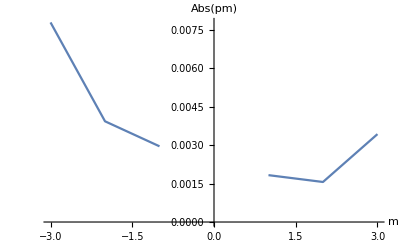

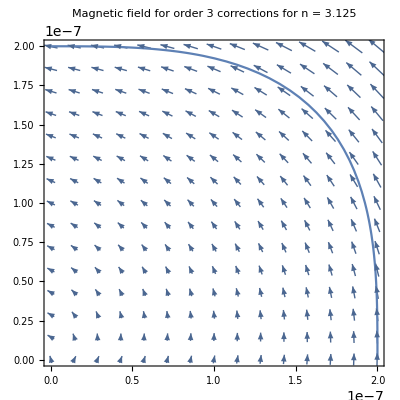

```mathematica
Block[
{M,R,λ,n,Ja,Jb,θ,Br,Bθ,B0,eqn,soln,p,m,k},
M=3;(* Scale of the number of coefficients *)
n=3.125;(* Curvature exponent *)
R=200*10^(-9);(* Size of the conveyor belt cavity *)
λ=110*10^(-9);(* London penetration depth of MgB2 (magnesium diboride) in 4.8 mT and 10.8 K *)
B0=4.8*10^(-3);(* Central magnetic field B0 = 4.8 mT *)
Ja=<||>;Jb=<||>;
For[
k=1,k≤2M,k++,
For[
m=-M,m≤M,m++,Ja=Append[Ja,{m,k}->NIntegrate[BesselI[m,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[I(m-k)θ],{θ,0,2π},Method->"RiemannRule"]];
];
Jb=Append[Jb,k->NIntegrate[BesselI[0,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},Method->"RiemannRule"]];
];
eqn=Table[Jb[k]B0/2+Total[Drop[Table[p[m]Ja[{m,k}],{m,-M,M}],{M+1}]]==0,{k,1,2M}];
soln=NSolve[eqn,Drop[Table[p[m],{m,-M,M}],{M+1}]];
Print[soln];
Print[ListLinePlot[Table[{m,Abs[Part[p[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(pm)"}]];
Br[x_,y_]:=Part[B0/2BesselI[0,Sqrt[x^2+y^2]/λ]+Total[Drop[Table[p[m]BesselI[m,Sqrt[x^2+y^2]/λ]Exp[I m ArcTan[x,y]],{m,-M,M}],{M+1}]]/.soln,1];
Bθ[x_,y_]:=Sqrt[3]B0/2BesselI[0,Sqrt[x^2+y^2]/λ];
Show[VectorPlot[{Re[(Br[x,y] x-Bθ[x,y] y)/Sqrt[x^2+y^2]],Re[(Br[x,y] y+Bθ[x,y] x)/Sqrt[x^2+y^2]]},{x,0.001R,0.999R},{y,0.001R,0.999R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Magnetic field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.50938}. NIntegrate obtained -0.000019803-0.000230118 ⅈ and 0.00429672 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.50938}. NIntegrate obtained 0.000218098-0.000293022 ⅈ and 0.00680529 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained -0.000207862-0.00311733 ⅈ and 0.028597 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{p[-4]→0.0766022+0.126771 ⅈ,p[-3]→0.0394593-0.0541256 ⅈ,p[-2]→-0.0120498-0.00538162 ⅈ,p[-1]→-0.00413851-0.00296522 ⅈ,p[1]→-0.00347729+0.00345736 ⅈ,p[2]→0.00252714+0.00259665 ⅈ,p[3]→-0.0161282-0.0148098 ⅈ,p[4]→0.0120968+0.00419359 ⅈ}}

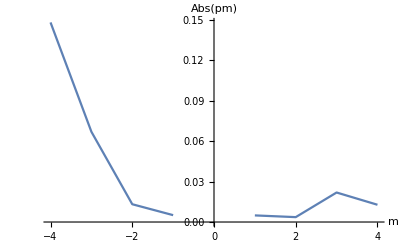

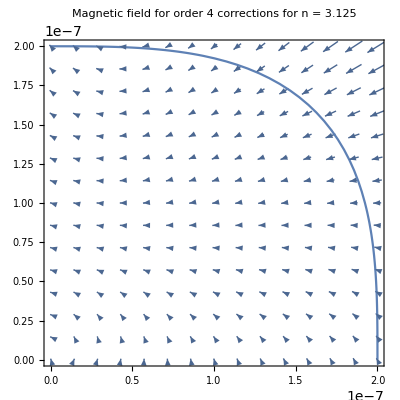

```mathematica
Block[
{M,R,λ,n,Ja,Jb,θ,Br,Bθ,B0,eqn,soln,p,m,k},
M=4;(* Scale of the number of coefficients *)
n=3.125;(* Curvature exponent *)
R=200*10^(-9);(* Size of the conveyor belt cavity *)
λ=110*10^(-9);(* London penetration depth of MgB2 (magnesium diboride) in 4.8 mT and 10.8 K *)
B0=4.8*10^(-3);(* Central magnetic field B0 = 4.8 mT *)
Ja=<||>;Jb=<||>;
For[
k=1,k≤2M,k++,
For[
m=-M,m≤M,m++,Ja=Append[Ja,{m,k}->NIntegrate[BesselI[m,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[I(m-k)θ],{θ,0,2π},Method->"RiemannRule"]];
];
Jb=Append[Jb,k->NIntegrate[BesselI[0,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},Method->"RiemannRule"]];
];
eqn=Table[Jb[k]B0/2+Total[Drop[Table[p[m]Ja[{m,k}],{m,-M,M}],{M+1}]]==0,{k,1,2M}];
soln=NSolve[eqn,Drop[Table[p[m],{m,-M,M}],{M+1}]];
Print[soln];
Print[ListLinePlot[Table[{m,Abs[Part[p[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(pm)"}]];
Br[x_,y_]:=Part[B0/2BesselI[0,Sqrt[x^2+y^2]/λ]+Total[Drop[Table[p[m]BesselI[m,Sqrt[x^2+y^2]/λ]Exp[I m ArcTan[x,y]],{m,-M,M}],{M+1}]]/.soln,1];
Bθ[x_,y_]:=Sqrt[3]B0/2BesselI[0,Sqrt[x^2+y^2]/λ];
Show[VectorPlot[{Re[(Br[x,y] x-Bθ[x,y] y)/Sqrt[x^2+y^2]],Re[(Br[x,y] y+Bθ[x,y] x)/Sqrt[x^2+y^2]]},{x,0.001R,0.999R},{y,0.001R,0.999R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Magnetic field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 3.72454×10^-6-0.00166146 ⅈ and 0.0139668 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 9.21117×10^-6-0.00595028 ⅈ and 0.0565829 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained -1.18942×10^-6-0.0023281 ⅈ and 0.0201553 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{p[-2]→-0.00196833-0.00130346 ⅈ,p[-1]→-0.00030373+0.000264354 ⅈ,p[1]→-0.000597453+0.000173628 ⅈ,p[2]→0.000704606+0.0000607967 ⅈ}}

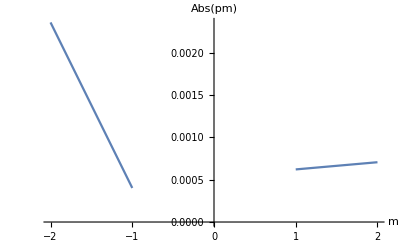

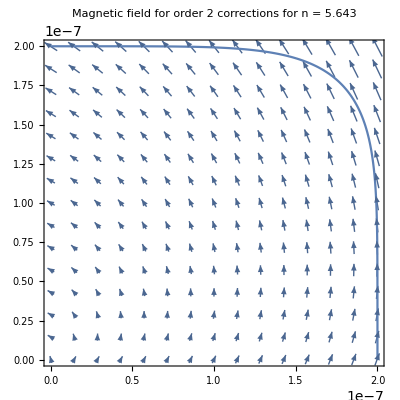

```mathematica
Block[
{M,R,λ,n,Ja,Jb,θ,Br,Bθ,B0,eqn,soln,p,m,k},
M=2;(* Scale of the number of coefficients *)
n=5.643;(* Curvature exponent *)
R=200*10^(-9);(* Size of the conveyor belt cavity *)
λ=110*10^(-9);(* London penetration depth of MgB2 (magnesium diboride) in 4.8 mT and 10.8 K *)
B0=4.8*10^(-3);(* Central magnetic field B0 = 4.8 mT *)
Ja=<||>;Jb=<||>;
For[
k=1,k≤2M,k++,
For[
m=-M,m≤M,m++,Ja=Append[Ja,{m,k}->NIntegrate[BesselI[m,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[I(m-k)θ],{θ,0,2π},Method->"RiemannRule"]];
];
Jb=Append[Jb,k->NIntegrate[BesselI[0,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},Method->"RiemannRule"]];
];
eqn=Table[Jb[k]B0/2+Total[Drop[Table[p[m]Ja[{m,k}],{m,-M,M}],{M+1}]]==0,{k,1,2M}];
soln=NSolve[eqn,Drop[Table[p[m],{m,-M,M}],{M+1}]];
Print[soln];
Print[ListLinePlot[Table[{m,Abs[Part[p[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(pm)"}]];
Br[x_,y_]:=Part[B0/2BesselI[0,Sqrt[x^2+y^2]/λ]+Total[Drop[Table[p[m]BesselI[m,Sqrt[x^2+y^2]/λ]Exp[I m ArcTan[x,y]],{m,-M,M}],{M+1}]]/.soln,1];
Bθ[x_,y_]:=Sqrt[3]B0/2BesselI[0,Sqrt[x^2+y^2]/λ];
Show[VectorPlot[{Re[(Br[x,y] x-Bθ[x,y] y)/Sqrt[x^2+y^2]],Re[(Br[x,y] y+Bθ[x,y] x)/Sqrt[x^2+y^2]]},{x,0.001R,0.999R},{y,0.001R,0.999R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Magnetic field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 0.000327983-0.000497723 ⅈ and 0.00526491 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 3.72454×10^-6-0.00166146 ⅈ and 0.0139668 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 9.21117×10^-6-0.00595028 ⅈ and 0.0565829 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{p[-3]→-0.0146361+0.018915 ⅈ,p[-2]→0.014578-0.00922129 ⅈ,p[-1]→-0.00234572+0.00180504 ⅈ,p[1]→0.00117913+0.00030853 ⅈ,p[2]→-0.00331379+0.000801268 ⅈ,p[3]→0.00778746-0.00263991 ⅈ}}

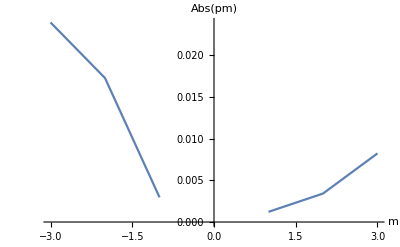

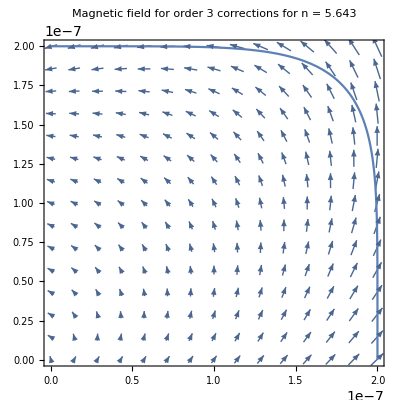

```mathematica
Block[
{M,R,λ,n,Ja,Jb,θ,Br,Bθ,B0,eqn,soln,p,m,k},
M=3;(* Scale of the number of coefficients *)
n=5.643;(* Curvature exponent *)
R=200*10^(-9);(* Size of the conveyor belt cavity *)
λ=110*10^(-9);(* London penetration depth of MgB2 (magnesium diboride) in 4.8 mT and 10.8 K *)
B0=4.8*10^(-3);(* Central magnetic field B0 = 4.8 mT *)
Ja=<||>;Jb=<||>;
For[
k=1,k≤2M,k++,
For[
m=-M,m≤M,m++,Ja=Append[Ja,{m,k}->NIntegrate[BesselI[m,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[I(m-k)θ],{θ,0,2π},Method->"RiemannRule"]];
];
Jb=Append[Jb,k->NIntegrate[BesselI[0,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},Method->"RiemannRule"]];
];
eqn=Table[Jb[k]B0/2+Total[Drop[Table[p[m]Ja[{m,k}],{m,-M,M}],{M+1}]]==0,{k,1,2M}];
soln=NSolve[eqn,Drop[Table[p[m],{m,-M,M}],{M+1}]];
Print[soln];
Print[ListLinePlot[Table[{m,Abs[Part[p[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(pm)"}]];
Br[x_,y_]:=Part[B0/2BesselI[0,Sqrt[x^2+y^2]/λ]+Total[Drop[Table[p[m]BesselI[m,Sqrt[x^2+y^2]/λ]Exp[I m ArcTan[x,y]],{m,-M,M}],{M+1}]]/.soln,1];
Bθ[x_,y_]:=Sqrt[3]B0/2BesselI[0,Sqrt[x^2+y^2]/λ];
Show[VectorPlot[{Re[(Br[x,y] x-Bθ[x,y] y)/Sqrt[x^2+y^2]],Re[(Br[x,y] y+Bθ[x,y] x)/Sqrt[x^2+y^2]]},{x,0.001R,0.999R},{y,0.001R,0.999R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Magnetic field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 6.70393×10^-7-0.00011851 ⅈ and 0.00162837 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 0.000327983-0.000497723 ⅈ and 0.00526491 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 3.72454×10^-6-0.00166146 ⅈ and 0.0139668 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{p[-4]→0.00468092-0.0322255 ⅈ,p[-3]→0.00663586+0.000394427 ⅈ,p[-2]→-0.00779527+0.000877102 ⅈ,p[-1]→0.000317687-0.000108676 ⅈ,p[1]→-0.00115435-0.0000919627 ⅈ,p[2]→0.00349066+0.000346573 ⅈ,p[3]→-0.00956483-0.000482392 ⅈ,p[4]→0.0176506+0.00552354 ⅈ}}

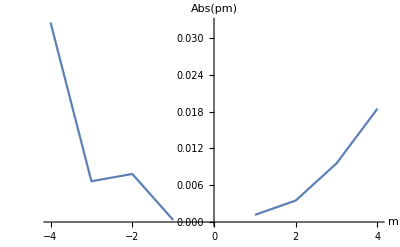

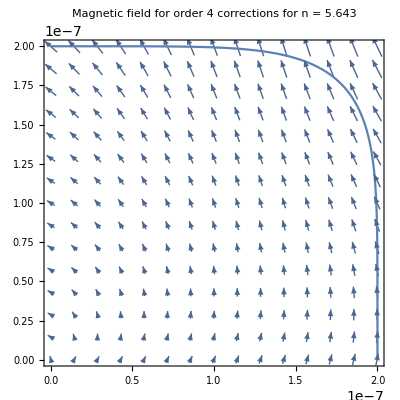

```mathematica
Block[
{M,R,λ,n,Ja,Jb,θ,Br,Bθ,B0,eqn,soln,p,m,k},
M=4;(* Scale of the number of coefficients *)
n=5.643;(* Curvature exponent *)
R=200*10^(-9);(* Size of the conveyor belt cavity *)
λ=110*10^(-9);(* London penetration depth of MgB2 (magnesium diboride) in 4.8 mT and 10.8 K *)
B0=4.8*10^(-3);(* Central magnetic field B0 = 4.8 mT *)
Ja=<||>;Jb=<||>;
For[
k=1,k≤2M,k++,
For[
m=-M,m≤M,m++,Ja=Append[Ja,{m,k}->NIntegrate[BesselI[m,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[I(m-k)θ],{θ,0,2π},Method->"RiemannRule"]];
];
Jb=Append[Jb,k->NIntegrate[BesselI[0,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},Method->"RiemannRule"]];
];
eqn=Table[Jb[k]B0/2+Total[Drop[Table[p[m]Ja[{m,k}],{m,-M,M}],{M+1}]]==0,{k,1,2M}];
soln=NSolve[eqn,Drop[Table[p[m],{m,-M,M}],{M+1}]];
Print[soln];
Print[ListLinePlot[Table[{m,Abs[Part[p[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(pm)"}]];
Br[x_,y_]:=Part[B0/2BesselI[0,Sqrt[x^2+y^2]/λ]+Total[Drop[Table[p[m]BesselI[m,Sqrt[x^2+y^2]/λ]Exp[I m ArcTan[x,y]],{m,-M,M}],{M+1}]]/.soln,1];
Bθ[x_,y_]:=Sqrt[3]B0/2BesselI[0,Sqrt[x^2+y^2]/λ];
Show[VectorPlot[{Re[(Br[x,y] x-Bθ[x,y] y)/Sqrt[x^2+y^2]],Re[(Br[x,y] y+Bθ[x,y] x)/Sqrt[x^2+y^2]]},{x,0.001R,0.999R},{y,0.001R,0.999R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Magnetic field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 1.46377×10^-7-0.0000172561 ⅈ and 0.000474205 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 6.70393×10^-7-0.00011851 ⅈ and 0.00162837 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 0.000327983-0.000497723 ⅈ and 0.00526491 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{p[-5]→-0.0227243-0.0683456 ⅈ,p[-4]→0.0016369+0.0113505 ⅈ,p[-3]→0.00502235+0.0018684 ⅈ,p[-2]→-0.00331471-0.00404635 ⅈ,p[-1]→-0.000334169+0.000350343 ⅈ,p[1]→-0.000891846+0.000307828 ⅈ,p[2]→0.0016099-5.15894×10^-6 ⅈ,p[3]→-0.00246989-0.00205716 ⅈ,p[4]→0.00272008+0.00920428 ⅈ,p[5]→0.0141166-0.0149624 ⅈ}}

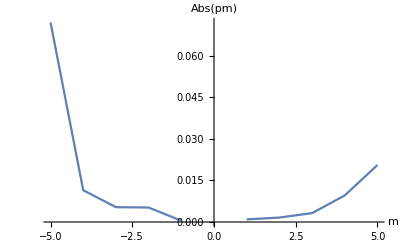

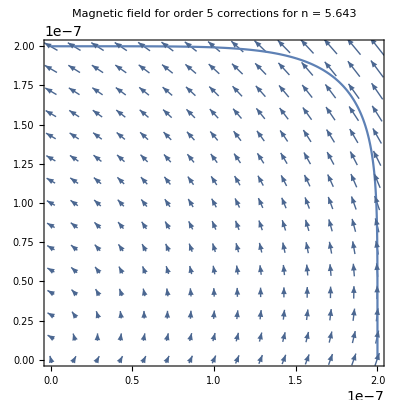

```mathematica
Block[
{M,R,λ,n,Ja,Jb,θ,Br,Bθ,B0,eqn,soln,p,m,k},
M=5;(* Scale of the number of coefficients *)
n=5.643;(* Curvature exponent *)
R=200*10^(-9);(* Size of the conveyor belt cavity *)
λ=110*10^(-9);(* London penetration depth of MgB2 (magnesium diboride) in 4.8 mT and 10.8 K *)
B0=4.8*10^(-3);(* Central magnetic field B0 = 4.8 mT *)
Ja=<||>;Jb=<||>;
For[
k=1,k≤2M,k++,
For[
m=-M,m≤M,m++,Ja=Append[Ja,{m,k}->NIntegrate[BesselI[m,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[I(m-k)θ],{θ,0,2π},Method->"RiemannRule"]];
];
Jb=Append[Jb,k->NIntegrate[BesselI[0,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},Method->"RiemannRule"]];
];
eqn=Table[Jb[k]B0/2+Total[Drop[Table[p[m]Ja[{m,k}],{m,-M,M}],{M+1}]]==0,{k,1,2M}];
soln=NSolve[eqn,Drop[Table[p[m],{m,-M,M}],{M+1}]];
Print[soln];
Print[ListLinePlot[Table[{m,Abs[Part[p[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(pm)"}]];
Br[x_,y_]:=Part[B0/2BesselI[0,Sqrt[x^2+y^2]/λ]+Total[Drop[Table[p[m]BesselI[m,Sqrt[x^2+y^2]/λ]Exp[I m ArcTan[x,y]],{m,-M,M}],{M+1}]]/.soln,1];
Bθ[x_,y_]:=Sqrt[3]B0/2BesselI[0,Sqrt[x^2+y^2]/λ];
Show[VectorPlot[{Re[(Br[x,y] x-Bθ[x,y] y)/Sqrt[x^2+y^2]],Re[(Br[x,y] y+Bθ[x,y] x)/Sqrt[x^2+y^2]]},{x,0.001R,0.999R},{y,0.001R,0.999R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Magnetic field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```